```mathematica
a1={1,0,0};
a2={0,1,0};
a3={0,0,1};
latt=Flatten[Table[n1*a1+n2*a2+n3*a3,{n1,-10,10},{n2,-10,10},{n3,-10,10}],2];
norms = Norm[#]&/@latt;
order=Ordering[norms];
norms=norms[[order]];
latt=latt[[order]];
(*latt=latt[[;;400]];*)
```

```mathematica
f[qx_,qy_]=Sum[ⅇ^(ⅈ {qx, qy}.{x,y}),{x,latt[[;;,1]]},{y,latt[[;;,2]]}];
```

$Aborted

```mathematica
DensityPlot[f[N[π qx],N[π qy]]//Re,{qx,-1,1},{qy,-1,1},PlotRange->Full,PlotPoints->50,PlotLegends->Automatic]
```

-Graphics-

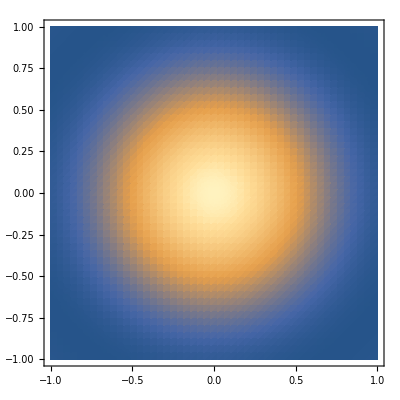

```mathematica
Clear[f]
f3[qx_,qy_,qz_]:=NIntegrate[ⅇ^(ⅈ qx *(x1-x2))ⅇ^(ⅈ qy*(y1-y2))ⅇ^(ⅈ qz*(z1-z2)),{x1,y1,z1}∈Ball[],{x2,y2,z2}∈Ball[]]
DensityPlot[f2[N[qx π],N[qy π]],{qx,-1,1},{qy,-1,1},PlotRange->Full,PlotPoints->50]
```

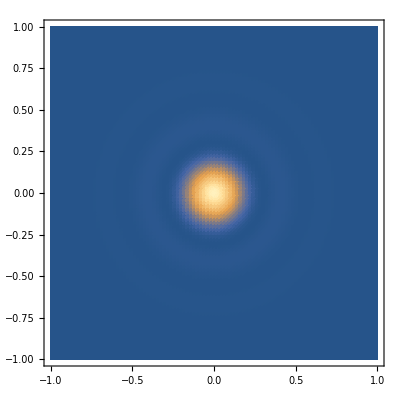

```mathematica
DensityPlot[BesselJ[2/2,4Norm[π{x,y}]]^2/(4Norm[π{x,y}])^2,{x,-1,1},{y,-1,1},PlotRange->Full,PlotPoints->100]
```

```mathematica
Limit[BesselJ[2/2,R Norm[π{q,0}]]/(R Norm[π{q,0}]),q->0]
```

1/2

```mathematica
f2[N[qx π],N[0 π]]
```

π^2 Hypergeometric0F1Regularized[2,1/4 (0.-9.8696 qx^2)]^2

```mathematica
4Limit[(BesselJ[2/2,R Norm[π{qx,0}]]/(R Norm[π{qx,0}]))^2,{qx->0}]
```

1

```mathematica
Limit[f2[N[qx π],N[0 π]],qx->0]
```

157.914

191.945 Hypergeometric0F1Regularized[2,-441/400 (qx^2+qy^2)]^2

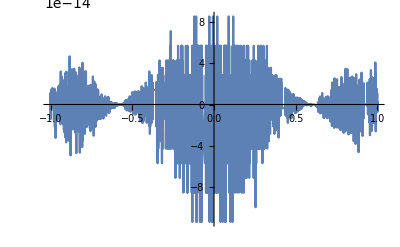

```mathematica
R=2.1;
f2[qx_,qy_]=Integrate[ⅇ^(ⅈ qx *(x1-x2))ⅇ^(ⅈ qy*(y1-y2)),{x1,y1}∈Disk[{0,0},R],{x2,y2}∈Disk[{0,0},R]]
Plot[f2[N[qx π],N[0 π]]-(2π R^2 BesselJ[2/2,R Norm[π{qx,0}]]/(R Norm[π{qx,0}]))^2,{qx,-1,1},PlotRange->Full,PlotPoints->100]
```

```mathematica
Integrate[ⅇ^(ⅈ qx *x)ⅇ^(ⅈ qy *y)ⅇ^(ⅈ qz*z),{x,y,z}∈Ball[],Assumptions->qx∈Reals&&qy∈Reals&&qz∈Reals]
```

$Aborted

```mathematica
Integrate[ⅇ^(ⅈ qx *x1)ⅇ^(ⅈ qy*y1),{x1,y1}∈Disk[{0,0},R]]Integrate[ⅇ^(ⅈ qx *x1)ⅇ^(ⅈ qy*y1),{x1,y1}∈Disk[{0,0},R]]
%/.{qx->0,qy->0}
```

π^2 Hypergeometric0F1Regularized[2,1/4 (-qx^2-qy^2)]^2

π^2

```mathematica
Integrate[ⅇ^(ⅈ qx *x1)ⅇ^(ⅈ qy*y1)ⅇ^(ⅈ qz*z1),{x1,y1,z1}∈Ball[]]
```

2 π Integrate[ⅇ^(ⅈ qx Region`RegionIntegrateDump`s Cos[Region`RegionIntegrateDump`t[1]]) (Region`RegionIntegrateDump`s)^2 BesselJ[0,√(qy^2+qz^2) Region`RegionIntegrateDump`s Sin[Region`RegionIntegrateDump`t[1]]] Sin[Region`RegionIntegrateDump`t[1]],{Region`RegionIntegrateDump`s,0,1},{Region`RegionIntegrateDump`t[1],0,π},GenerateConditions→False,Assumptions→True]